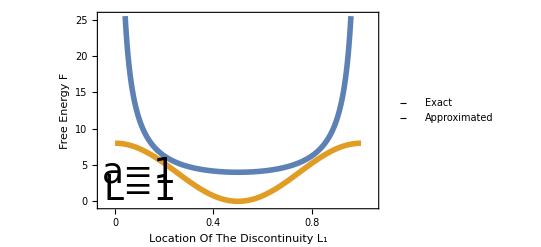

```mathematica
F[a_,L_,L1_]:=a^2/L1+a^2/(L-L1);
F2[a_,L_,L1_]:=(8×a^2)/L×(Cos[(π×L1)/L])^2
Plot[{F[1,1,x],F2[1,1,x]},{x,0,1},PlotStyle->{Thickness[0.01]}, Frame->{True, True, True, True},FrameTicks->{{{0,5,10,15,20,25},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{-0.05,1.05},{-0.5,25.5}},FrameLabel->{{"Free Energy F", None},{"Location Of The Discontinuity L_1", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Exact","Approximated"},LegendMarkers->{{Graphics[Rectangle[{1,1},{10,2}]],80},{Graphics[Rectangle[{1,1},{10,2}]],80}}],{Center, Top}],Epilog->{Text[Style["a=1",Directive[Black,36]],{0.1,4}],Text[Style["L=1",Directive[Black,36]],{0.1,1.5}]}]
```

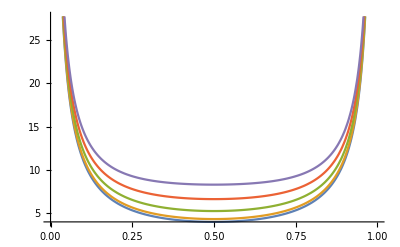

```mathematica
F3[a_,L_,L1_,A_]:=a^2×A×(ⅇ^(A×L1)+ⅇ^(-A×L1))/(ⅇ^(A×L1)-ⅇ^(-A×L1))+a^2×A×(ⅇ^(2×A×L-A×L1)+ⅇ^(A×L1))/(ⅇ^(2×A×L-A×L1)-ⅇ^(A×L1));
Plot[{F[1,1,x],F3[1,1,x,1],F3[1,1,x,2],F3[1,1,x,3],F3[1,1,x,4]},{x,0,1}]
```

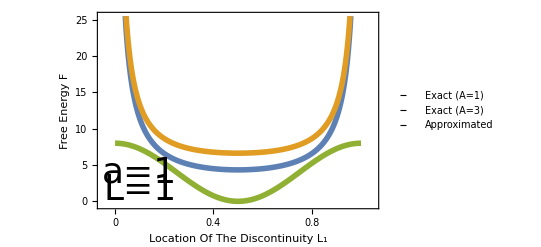

```mathematica
Plot[{F3[1,1,x,1],F3[1,1,x,3],F2[1,1,x]},{x,0,1},PlotStyle->{Thickness[0.01]}, Frame->{True, True, True, True},FrameTicks->{{{0,5,10,15,20,25},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{-0.05,1.05},{-0.5,25.5}},FrameLabel->{{"Free Energy F", None},{"Location Of The Discontinuity L_1", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Exact (A=1)","Exact (A=3)","Approximated"},LegendMarkers->{{Graphics[Rectangle[{1,1},{10,2}]],80},{Graphics[Rectangle[{1,1},{10,2}]],80},{Graphics[Rectangle[{1,1},{10,2}]],80}}],{Center, Top}],Epilog->{Text[Style["a=1",Directive[Black,36]],{0.1,4}],Text[Style["L=1",Directive[Black,36]],{0.1,1.5}]}]
```